Seth AbuHamdeh

ID:34937889

Problem 1

```mathematica
a = {1,0};
b = {-1,0};
c = {0,1};
d = {0,-1};
randomStep := RandomChoice[{a,b,c,d}]
```

```mathematica
Table[randomStep,{10}];
```

{{1,0},{0,-1},{0,1},{0,1},{0,1},{0,-1},{0,1},{-1,0},{1,0},{0,-1}}

Problem 2

```mathematica
walk2D[n_] := NestList[#+randomStep&,{0,0},n]
```

```mathematica
walk2D[10]
```

{{0,0},{1,0},{1,1},{1,0},{1,-1},{2,-1},{2,0},{1,0},{2,0},{1,0},{1,1}}

Problem 3

0

11362

1174

0

29823

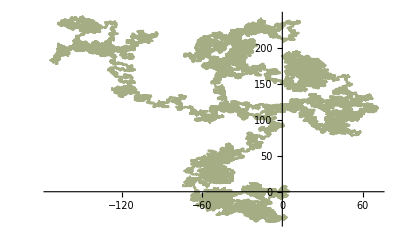

```mathematica
myWalk = walk2D[40000];
Count[myWalk,{50,50}]
Count[myWalk,pt_/; pt[[1]] < -50]
Count[myWalk, pt2_ /; pt2[[1]] > 50]
Count[myWalk, pt3_ /; pt3[[2]] < -50]
Count[myWalk, pt4_ /; pt4[[2]] > 50]
ListLinePlot[myWalk, ColorFunction->"StarryNightColors"]
```

Problem 4: Largest count was part f meaning majority of walk was above 50 on y-axis as seen as the majority of the graph was above 50.

Lowest was part d reflected on graph as none of the graph went below y level -50.

1

0

0